```mathematica
h=3
```

3

```mathematica
2.0
```

2.

```mathematica
T1=NDSolve[{r''[t]-r[t] theta'[t]^2-h Cos[theta[t]]+r[t]-1==0,r[t]theta''[t]+2 r'[t] theta'[t]+h Sin[theta[t]]==0,theta[0]==-Pi/2,theta'[0]==0,r'[0]==0,r[0]==1},{theta[t],r[t]},{t,0,100}]
```

{{theta[t]→InterpolatingFunction[{{0.,100.}},<>][t],r[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

```mathematica
solution1:=T1[[1,2,2]]
```

```mathematica
solution2:=T1[[1,1,2]]
```

```mathematica
FullForm[solution1]
```

solution1

```mathematica
NSolve[h s==(s-1)^2,s]
```

{{s→0.208712},{s→4.79129}}

```mathematica
rho[x]:=solution1/.t->x
```

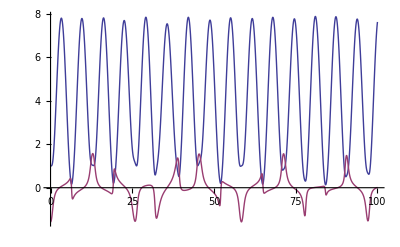

```mathematica
Plot[{solution1,solution2},{t,0,100}]
```

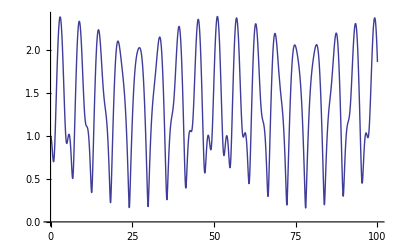

```mathematica
Plot[solution,{t,0,100}]
```